# Solving a pendulum ODE

## Solution

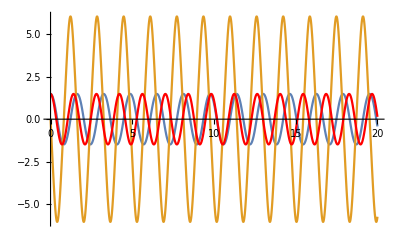

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
g=20;                         (*acceleration of gravity, m/s^2*)
l=1;                            (*length of pendulum, in meters*)
finaltime=20;       (*Final time of the simulation, in seconds*)  
startang=85*Pi/180;  (*The initial start angle.  Play around with this. Compare the actual solution to the approximate one*)

(*Solve the 2nd Order DE*)
eq1=y''[t]==-g/l Sin[y[t]];
eq2 = y'[0]==0;
eq3= y[0]==startang;
s=NDSolve[{eq1,eq2,eq3}, {y,y'},{t,0,finaltime}];

(*Replace rules solution with functions of angular positon and velocity*)
{theta[t_],omega[t_]}={y[t],y'[t]}/.s//Flatten;

(*Plot angular positon and velocity AND approximate solution*)
plot1=Plot[{theta[t],omega[t]},{t,0,finaltime}];
plot2=Plot[startang*Cos[Sqrt[g/l] t],{t,0,finaltime},PlotStyle->{Red}];
Show[plot1,plot2]

(*Find x,y positon for graphics*)
x[t_]=l*Sin[theta[t]];
y[t_]=-l*Cos[theta[t]];

(*Make an animation of the pendulum's motion*)
Animate[
Graphics[{Disk[{x[t],y[t]},.05],Line[{{0,0},{x[t],y[t]}}]},PlotRange->{{-1.5,1.5},{-1,0}}],
{t,0,finaltime},
AnimationRate->.3]
```

## Response

I started by varying the starting angle, startang, from 40 degrees to 85 degrees. This slightly increased the oscillation period and nearly doubled the oscillation amplitude. This also increased the difference between the velocity and approximate solution curves. Keeping this change I then increased the gravitational acceleration to 20 m/s^2. This decreased the oscillation period. While I’m not sure if this increased the difference between the velocity and approximate solution curves it did reduce the oscillation period enough to show the two going into and out of phase over several oscillations.